## Fluidos que fluyen.

#### Latín

Fluidus -a -um: que corre | débil, lánguido | lacio, flojo, efímero. (-idus, sufijo que indica que es perceptible por la vista )

#### ¿Definición de fluido según Lai?

Un fluido es un material que no puede soportar esfuerzos de corte sin deformarse continuamente.

#### Todos los fluidos, el Fluido (newtoniano)

Es un fluido cuyo estado de esfuerzo depende no de la deformación, sino de la tasa de deformación.  Otras denominaciones: 

• Fluido linealmente viscoso

#### Tensor de esfuerzo de un fluido en reposo

Si no puede soportar esfuerzos de corte, cizalla o tangenciales, entonces en un punto -y en cualquier plano-, un fluido (en reposo) sólo debe tener esfuerzos normales, con lo cual cualquier vector n  es eingenvector de T:

							Tn = λn			(1)

Si es para cualquier vector n que se mantiene la relación (1), entonces es fácil probar que λ es igual para cualquier vector:

Tn_1 = λ_1  n_1             y                 Tn_2 = λ_2  n_2

n_2 · Tn_1 - n_1 · Tn_2 =( λ_1 - λ_2)   n_1· n_2     (2)


Usando la definición de tensor transpuesto n_1 · T n_2 = n_2 · T^T  n_1, con lo que el lado izquierdo de la expresión (2) es 0 y:

                                              λ_1 - λ_2 = 0   ∀ n_1, n_2   ⟹   λ_1 = λ_2 = λ
                                              
con lo cual un tensor en el cual todos los esfuerzos son normales (y compresivos) se escribe:

T = -p I = (-p | 0 | 0
0 | -p | 0
0 | 0 | -p)

lo que denominamos tensor de esfuerzo hidrostático.

#### Soy un pobre fluido al cual no dejan comprimir

La idea de fluido incompresible se usa bastante para ciertas situaciones, aunque todo depende de la escala:

•  El agua es considerada incompresible para los flujos que vamos a desarrollar...
•  El agua es considerada compresible para la transmisión de sonido....

Entonces, un fluido incompresible es aquél que nunca cambia la densidad:

								

y si vemos la ec. de conservación de la masa:

								-Graphics-
entonces, un fluido incompresible tiene una divergencia del campo de velocidades:

							  	⟹ 	 
							
quedando definido fluido incompresible.

Fíjense que div v = 0 no es otra cosa que: lo que entra por algunas de las caras de un cubito infinitesimal
sale por las otras caras del cubito infinitesimal...lo que deberían haber visto en todas las  derivaciones
de las ecs. de FísicaMatemática II.

## Resolviendo el problema de la hidrostática

Las ecuaciones de movimiento (en equilibrio, o sea, ecuaciones de inmovimiento) son:
								-Graphics-

Recordamos nuestro resultado:

 								-Graphics-
 								
con lo que la primera ecuación queda:

es decir, obtenemos una conexión entre las derivadas del escalar p(x) y las fuerzas de volumen.

Si suponemos un campo gravitatorio en la dirección e_3 para las fuerzas de volumen:

				-Graphics-

entonces las ecuaciones para la presión quedan:

				-Graphics-
				
que no es otra cosa que nuestras ecuaciones para la presión hidrostática tal cual la conocemos:

•  p(x_1 , x_2 , x_3 ) es función sólo de x_3 (depende de la altura en el campo gravitatorio)

### Práctico 6 - Solución

-Graphics-

Para resolver este ejercicio, recordamos que: 

•  Un fluído se define como aquel material que no soporta esfuerzos cortantes.
•  Las ec. que resolverá nuestro problema es la ecuación de movimiento sin movimiento:

```mathematica
B = {a1,a2,-g} (*a1 y a2 constantes*)
```

{a1,a2,-g}

la ecuación anterior define nuestras fuerzas de volumen. Hay que preguntarse si es válido considerar aceleraciones como fuerzas de volumen: no nos lo preguntamos más, es válido por el ppio de equivalencia de Einstein (gravedad y aceleraciones indiscernibles).

Entonces se puede escribir:
					 B = a_1 e_1 + a_2 e_2  + g e_3                  ó       B =    + g e_3      y     a =  -a_1 e_1 + -a_2 e_2

Si elegimos la primera tenemos:

∂T_ij/∂x_j + ρ  B_i = 0 


Y también sabemos que si el fluido está en reposo, entonces no hay deformaciones del mismo, i.e., estado isotrópico:
•  T_ij = p(x_1, x_2, x_3) δ_ij
•  Con lo anterior, decimos que resolvemos el estacionario directamente (nada tiene que ver con acelerar un fluído, sino con tenerlo acelerado un tiempo laaaaaarrrrgo).

Entonces con las ecs anteriores tenemos:

∂p(x_1, x_2, x_3) / ∂x_1 = - ρ a_1  (1)
∂p(x_1, x_2, x_3) / ∂x_2 = - ρ a_2  (2)
∂p(x_1, x_2, x_3) / ∂x_3 = - ρ g  (3)  

e integrando estas expresiones queda:
(1)    p_1 = - ρ a_1 x_1 + f_1(x_2, x_3)
(2)    p_2 = - ρ a_2 x_2 + f_1(x_1, x_3)
(3)    p_3 = - ρ  g   x_3 + f_3(x_1, x_2)

ojo que las f_i son las otras p...por lo que nos queda:

p = -ρ (a_1 x_1 + a_2 x_2 -g x_3) + c

y obviamente podemos hacer c = p_o, la presión atmosférica. Finalmente tenemos:
p = -ρ (a_1 x_1 + a_2 x_2 -g x_3) + p_o

la otra cuestión es que x_3 está definido en el sentido contrario de la gravedad, así es que hacer crecer x_3 es hacer decrecer la presión.
Si consideramos las a_i = 0, entonces nos queda la ecuación que todes conocemos de hidrostática.

Notar que el Lai parece estar mal sobre la dependencia del campo de presión que aparece en el fluido....no está mal, pero normaliza la interpretación (página 357).

Un remark más: este problema se puede resolver como el del Lai, cambiando las coordenadas para que la aceleración perpendicular a la gravedad quede en un sólo eje.

### Recordando cosas

Tenemos que un fluido en reposo ó, más generalmente, en movimiento de cuerpo rígido,  tiene sólo un tensor isotrópico cuyo autovalor es la presión p del fluído. Obvio que es una cuestión puntual, i.e., p ≡ p(x_i).

La cuestión de la isotropía del tensor esfuerzo no se mantiene para fluidos que no están en reposo o en movimiento de cuerpo rígido... el chiste que se usa habitualmente es partir el tensor de esfuerzos en una parte isotrópica (que corresponde al reposo o al cuerpo rígido) y otra que no lo es:


donde en la ec. anterior vamos a tener que el tensor T'_ij va a ser la componente que modele los esfuerzos del fluído en movimiento.

Se definen entonces los fluídos newtonianos  como una clase de materiales idealizados:

•  Para cada punto material, T'_ij depende sólo del tensor tasa de deformación  (y no del tensor deformación....un fluido adopta la forma del recipiente que lo contiene). El tensor tasa de deformación puede ser escrito en función del campo de velocidades del fluido como:

-Graphics-

•  El fluido es isotrópico respecto de cualquier configuración de referencia.

Siguiendo argumentos parecidos a los del SLEI (muchos y muy importantes), y teniendo en cuenta que Δ = D_11 + D_22 + D_33 = D_kk, tenemos que T'_ij está dado por:

-Graphics-

donde λ y μ son constantes (distintas del SLEI) que tienen dimensiones [fuerza][tiempo]/[longitud^2]. El tensor T_ij se denomina el tensor de esfuerzo viscoso. El esfuerzo total, entonces, estará dado por:



v.g, dentro de la diagonal
-Graphics-
fuera:
-Graphics-

la presión seguirá dada por el escalar p, aunque dejará de ser el esfuerzo normal total en cualquier plano.

-Graphics-

{-x-y,x-y}

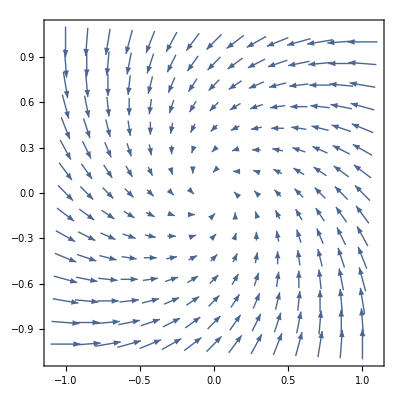

```mathematica
v = {-c(Subscript[x, 1] + Subscript[x, 2]), c(Subscript[x, 2] - Subscript[x, 1]), 0};
v2d = {-(x + y), (x - y)}
VectorPlot[v2d, {x,-1,1}, {y,-1,1}]
```

```mathematica
Print["v =  ",MatrixForm[v]]

Dr = 1/2*(Grad[v,{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}] +Transpose[Grad[v,{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]] ); 
Print["D = ",MatrixForm[Dr]]

Δ = Tr[Dr]; Print["Δ = ", MatrixForm[Δ]]
T' = λ 0 IdentityMatrix[3] + 2μ Dr; 
Print["T' = ",MatrixForm[T']]
```

v =  (-c (x_1+x_2)
c (-x_1+x_2)
0)

D = (-c | -c | 0
-c | c | 0
0 | 0 | 0)

Δ = 0

T' = (-2 c μ | -2 c μ | 0
-2 c μ | 2 c μ | 0
0 | 0 | 0)